## 用最短tour寻找最短超级排列

#### 长度为3

```mathematica
len=3
f[0]=len;
```

3

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]]
```

{123,132,213,231,312,321}

```mathematica
f[x_]/;x!=0:=x
dis[a_,b_]:=Block[{n=1,x,y},x=ToExpression@Characters[b];y=ToExpression@Characters[a];While[Take[x,n]!=Take[y,-n]&&n<len,n++];f[len-n]](*n个元素的全排列构成一个集合S，计算S中任意两个元素之间的距离，找到一个遍历所有元素的最短路线，就找到了一个最小超级排列*)
```

```mathematica
{slen,tour}=FindShortestTour[per,DistanceFunction->dis]
st=Drop[per[[tour]],-1]
```

{12,{1,6,2,3,5,4,1}}

{123,321,132,213,312,231}

```mathematica
FindShortestTour[{"123","132","213","231","312","321"}]
```

{12,{1,2,6,5,3,4,1}}

```mathematica
s1={"123","231","312","213","132","321"};(*len=3的真正的最优解*)
```

```mathematica
tourlen[t_]:=(dis@@@Partition[t,2,1]//Total)+len
```

```mathematica
tourlen/@{per,st,s1}
```

{15,13,9}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(123→321)→2
(321→132)→2
(132→213)→2
(213→312)→2
(312→231)→2
(231→123)→2

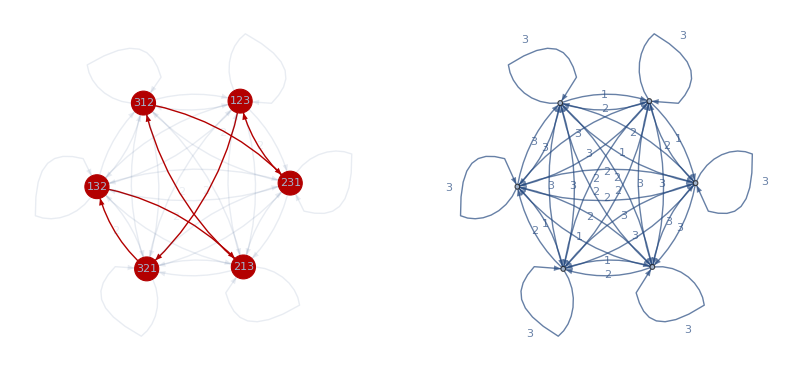

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

#### 长度为4

```mathematica
len=4
f[0]=len;
```

4

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]]
```

{1234,1243,1324,1342,1423,1432,2134,2143,2314,2341,2413,2431,3124,3142,3214,3241,3412,3421,4123,4132,4213,4231,4312,4321}

```mathematica
f[x_]/;x!=0:=x
dis[a_,b_]:=Block[{n=1,x,y},x=ToExpression@Characters[b];y=ToExpression@Characters[a];While[Take[x,n]!=Take[y,-n]&&n<len,n++];f[len-n]]
```

```mathematica
{slen,tour}=FindShortestTour[per,DistanceFunction->dis]
st=per[[Drop[%[[2]],-1]]]
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

{1234,3421,1342,4213,3142,2314,1423,4231,3214,1432,4321,2143,4312,1243,2431,3124,2134,3412,4123,3241,1324,2413,4132,2341}

```mathematica
tourlen[t_]:=(dis@@@Partition[t,2,1]//Total)+len
```

```mathematica
tourlen/@{per,st}
```

{93,55}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(1234→3421)→2
(3421→1342)→3
(1342→4213)→2
(4213→3142)→3
(3142→2314)→3
(2314→1423)→2
(1423→4231)→1
(4231→3214)→4
(3214→1432)→2
(1432→4321)→1
(4321→2143)→2
(2143→4312)→2
(4312→1243)→2
(1243→2431)→1
(2431→3124)→2
(3124→2134)→4
(2134→3412)→2
(3412→4123)→1
(4123→3241)→3
(3241→1324)→3
(1324→2413)→2
(2413→4132)→1
(4132→2341)→3
(2341→1234)→3

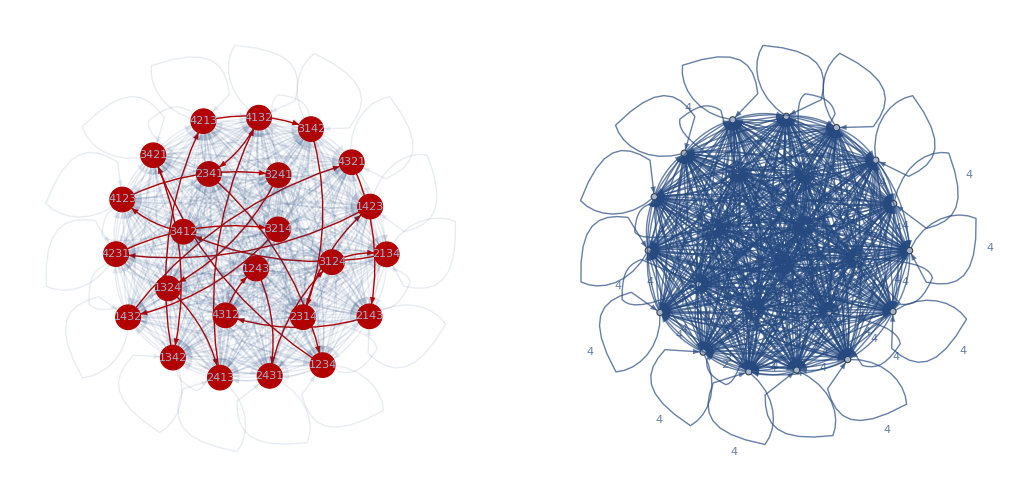

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .55,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

## 草稿

```mathematica
FindShortestTour
```

```mathematica
Graph
```

```mathematica
f[x_]:=x/.{y__,z_,z_,w__}:>{y,z,w}
```

```mathematica
f[Flatten/@(Permutations@Permutations[{1,2,3}])][[1;;10]]
```

{{1,2,3,1,3,2,1,3,2,3,1,3,1,2,3,2,1},{1,2,3,1,3,2,1,3,2,3,1,3,2,1,3,1,2},{1,2,3,1,3,2,1,3,3,1,2,2,3,1,3,2,1},{1,2,3,1,3,2,1,3,3,1,2,3,2,1,2,3,1},{1,2,3,1,3,2,1,3,3,2,1,2,3,1,3,1,2},{1,2,3,1,3,2,1,3,3,2,1,3,1,2,2,3,1},{1,2,3,1,3,2,3,1,2,1,3,3,1,2,3,2,1},{1,2,3,1,3,2,3,1,2,1,3,3,2,1,3,1,2},{1,2,3,1,3,2,3,1,3,1,2,2,1,3,3,2,1},{1,2,3,1,3,2,3,1,3,1,2,3,2,1,2,1,3}}

```mathematica
a={3,4,2,1};
b={1,2,3,4};
```

```mathematica
a={3,4,2,1};
b={4,3,2,1};
```

```mathematica
n=1;While[Take[a,n]!=Take[b,-n],n++]
```

```mathematica
n
```

4

```mathematica
Take[a,2]
```

{1,2}

```mathematica
k
```

```mathematica
Table[{Take[a,n],Take[b,-n]},{n,0,4}]
```

{{{},{}},{{3},{1}},{{3,4},{2,1}},{{3,4,2},{3,2,1}},{{3,4,2,1},{4,3,2,1}}}

```mathematica
Table[{Take[a,n]!=Take[b,-n]},{n,1,4}]
```

{{True},{True},{True},{True}}

```mathematica
Block
```

```mathematica
ToString/@Range[len]
```

{1,2,3,4,5}

```mathematica
dis["12345","45213"]
```

3

```mathematica
dis@@@Partition[s1]
```

```mathematica
dis
```

```mathematica
MapThread
```

```mathematica
Thread
```

```mathematica
Map
```

```mathematica
dis[st[[1]],st[[2]]]
```

1

```mathematica
shortestlist=per[[(%255)[[2]]]];
```

```mathematica
(%255)[[2]]//Length
```

721

```mathematica
n
```

4

```mathematica
ToString
```

```mathematica
ToExpression@Characters["1234"]
```

{1,2,3,4}

```mathematica
dis[a_,b_]:=Block[{n=1,x,y},While[Take[a,n]!=Take[b,-n]&&n<len,n++];n]
```

```mathematica
ToExpression[Characters@"1243"]
```

{1,2,4,3}

```mathematica
dis[{1,2,3,4},{1,2,4,3}]
```

ToExpression::notstrbox: Characters[1] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[2] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[3] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

1

```mathematica
dis["1234","2341"]
```

1

```mathematica
Table[dis[per[[i]],per[[i+1]]],{i,1,3!-1}]//Total
```

12

```mathematica
dis["1234","3421"]
```

3

```mathematica
n
```

4

```mathematica
dis[b,a]
```

4

```mathematica
n
```

5

```mathematica
d=SparseArray[{{1,2}->1,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->1,{4,3}->1,{4,5}->15,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];
```

```mathematica
d//MatrixForm
```

(∞ | 1 | ∞ | 1 | 1 | 1
1 | ∞ | 10 | ∞ | 1 | 1
∞ | 10 | ∞ | 1 | 1 | ∞
1 | ∞ | 1 | ∞ | 15 | ∞
1 | 1 | 1 | 15 | ∞ | ∞
1 | 1 | ∞ | ∞ | ∞ | ∞)

```mathematica
{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(dm[[#1,#2]]&)]
```

{12,{1,6,2,3,5,4,1}}

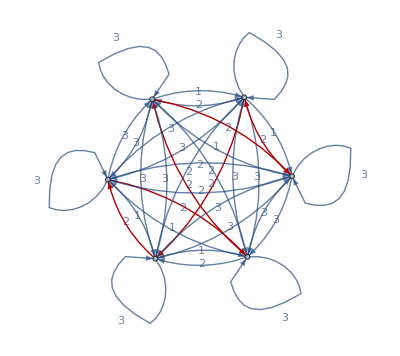

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"],{1->6,6->2,2->3,3->5,5->4,4->1}]
```

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
dm//MatrixForm
```

(4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 1 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 1 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1
4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 2 | 2 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 1 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4
4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 1 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 2 | 2 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4
1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 1 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 1 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4)

```mathematica
FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)]
st=per[[Drop[%[[2]],-1]]](*一种等效的写法*)
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

{1234,3421,1342,4213,3142,2314,1423,4231,3214,1432,4321,2143,4312,1243,2431,3124,2134,3412,4123,3241,1324,2413,4132,2341}

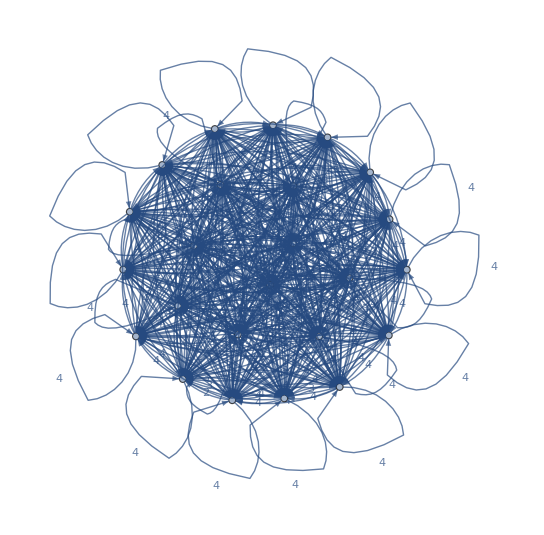

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight",VertexLabels->"Name"]
```

{105,{1,6,2,5,3,4,1}}

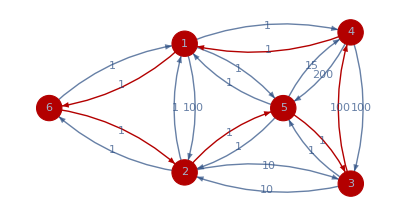

```mathematica
d=SparseArray[{{1,2}->100,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->100,{4,3}->100,{4,5}->200,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(d[[#1,#2]]&)]
HighlightGraph[WeightedAdjacencyGraph[d,EdgeLabels->"EdgeWeight",VertexSize-> .25,VertexLabels->Placed[Automatic,Center]],Graph[Rule@@@Partition[tour,2,1]]]
```

```mathematica
Partition[per[[tour]],2,1]
```

{{1234,3421},{3421,1342},{1342,4213},{4213,3142},{3142,2314},{2314,1423},{1423,4231},{4231,3214},{3214,1432},{1432,4321},{4321,2143},{2143,4312},{4312,1243},{1243,2431},{2431,3124},{3124,2134},{2134,3412},{3412,4123},{4123,3241},{3241,1324},{1324,2413},{2413,4132},{4132,2341},{2341,1234}}

```mathematica
dis@@@Partition[per[[tour]],2,1]
```

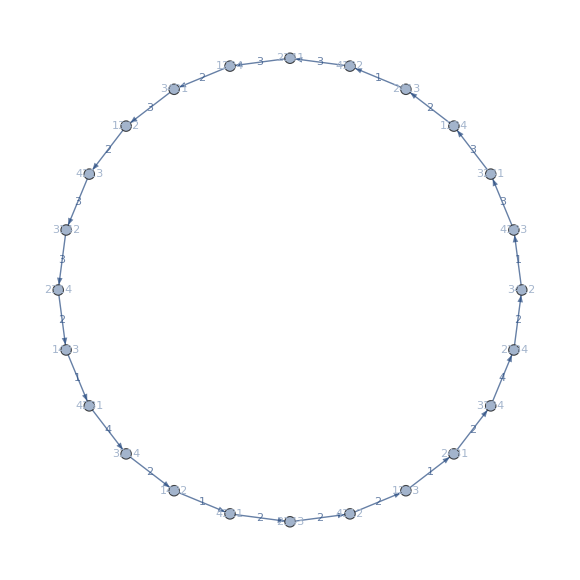

```mathematica
Graph[Rule@@@Partition[per[[tour]],2,1],EdgeLabels->Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Placed["Name",Center]]
```

```mathematica
Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]
```

{1→Placed[1234,Center],18→Placed[3421,Center],4→Placed[1342,Center],21→Placed[4213,Center],14→Placed[3142,Center],9→Placed[2314,Center],5→Placed[1423,Center],22→Placed[4231,Center],15→Placed[3214,Center],6→Placed[1432,Center],24→Placed[4321,Center],8→Placed[2143,Center],23→Placed[4312,Center],2→Placed[1243,Center],12→Placed[2431,Center],13→Placed[3124,Center],7→Placed[2134,Center],17→Placed[3412,Center],19→Placed[4123,Center],16→Placed[3241,Center],3→Placed[1324,Center],11→Placed[2413,Center],20→Placed[4132,Center],10→Placed[2341,Center]}

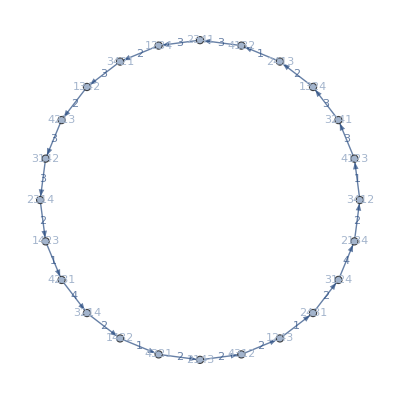

```mathematica
Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]]
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

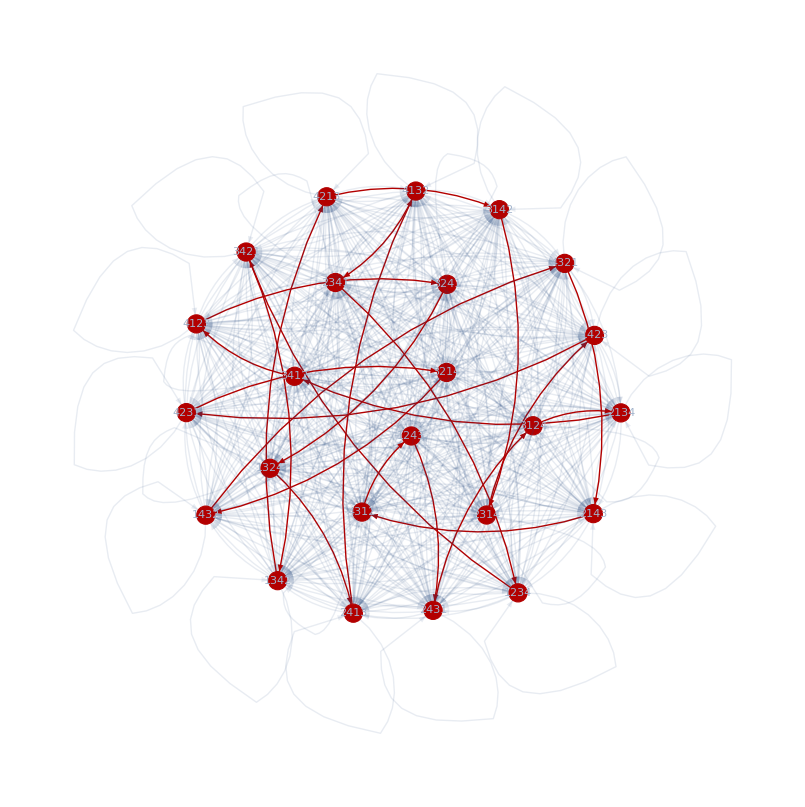

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]
```

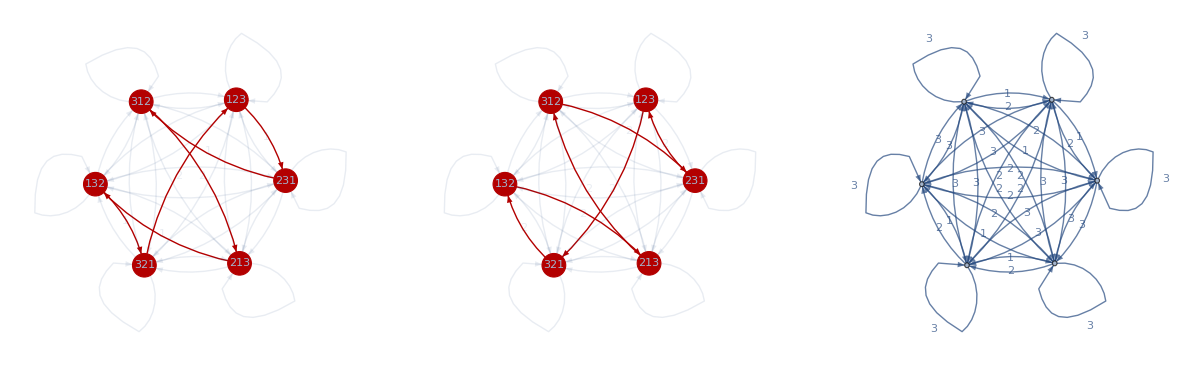

```mathematica
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]],VertexSize-> .25,VertexLabels->Table[stour3[[i]]->Placed[per[[stour3]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[stour3,2,1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]]]],

HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

```mathematica
s1~Join~{"123"}
```

{123,231,312,213,132,321,123}

```mathematica
stour3=Flatten@(Position[per,#]&/@(s1~Join~{"123"}))
```

{1,4,5,3,2,6,1}

```mathematica
tour
```

{1,6,2,3,5,4,1}